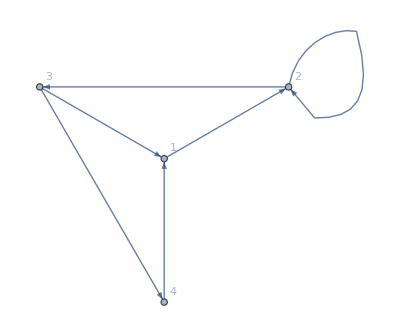

```mathematica
Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->All, GraphLayout->"RadialDrawing"]
```

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],4,2]
```

{4,1,2}

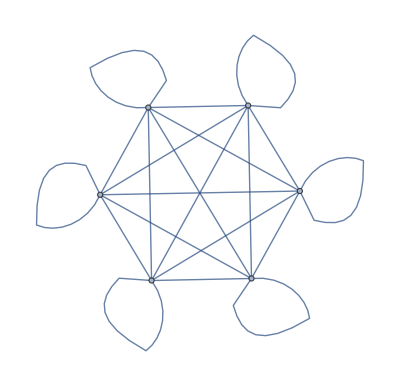

```mathematica
UndirectedGraph[Flatten[Table[i->j,{i,6},{j,6}]]]
```

```mathematica
Table[Graph[Table[RandomInteger[30]->RandomInteger[30], 50],VertexSize->0.4, ImageSize->200],6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CommunityGraphPlot[-Graphics-]
```

-Graphics-